```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2](1-Exp[(Ω0-ω)t])/(-I(Ω0-ω)) ,{ω,0,Infinity}]
```

∫_0^∞ (ⅈ ⅇ^(-ω/ωc) (1-ⅇ^(t (-ω+Ω0))) η ω Coth[(β ω)/2])/(-ω+Ω0)ⅆω

```mathematica
Ω0
```

1

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2] Sin[(Ω0-ω)t]/((Ω0-ω)/2) ,{ω,0,Infinity}]
```

∫_0^∞ (2 ⅇ^(-ω/ωc) η ω Coth[(β ω)/2] Sin[t (-ω+Ω0)])/(-ω+Ω0)ⅆω

```mathematica
FullSimplify[Cos[x]+Cos[y]]
```

Cos[x]+Cos[y]

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2] ,{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0&&Re[ωc]>0]

```mathematica
Integrate[η ω Exp[-ω/ωc],{ω,0,Infinity}]
```

ConditionalExpression[η ωc^2, Re[ωc]>0]

```mathematica
Integrate[η ω Coth[β ω/2] ,{ω,0,Infinity}]
```

∫_0^∞ η ω Coth[(β ω)/2]ⅆω

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[ω/2] ,{ω,0,Infinity}]
```

ConditionalExpression[0, Re[ωc]>0]

```mathematica
Integrate[η ω Exp[-ω]Coth[ω/2] ,{ω,0,Infinity}]
```

1/3 (-3+π^2) η

```mathematica
Integrate[η ω Exp[-ω]Coth[ω/2] ,{ω,0,Infinity}]
```

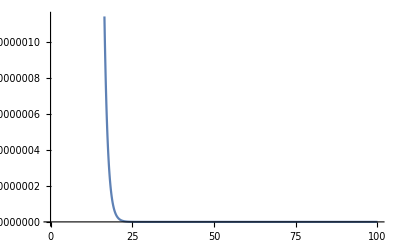

```mathematica
Plot[ω Exp[-ω]Coth[ω/2],{ω,0,100}]
```

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2]/(Exp[β ω]+1) ,{ω,0,Infinity}]
```

ConditionalExpression[(η Zeta[2,1+1/(β ωc)])/β^2, Re[β]>0&&Re[β+1/ωc]>0]

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2] ,{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0&&Re[ωc]>0]

```mathematica
Integrate[x Exp[-z x]/(1-Exp[-x]) ,{x,0,Infinity}]
```

ConditionalExpression[Zeta[2,z], Re[z]>0]

```mathematica
Integrate[x Exp[- x]/(1-Exp[-x]) ,{x,0,Infinity}]
```

π^2/6

```mathematica
N[Pi^2/6]
```

1.64493

```mathematica
NIntegrate[x Exp[- x]/(1-Exp[-x]) ,{x,0,Infinity}]
```

1.64493

```mathematica
Srwa[ηwc_,βwc_,ΩXwc_]:=2NIntegrate[NIntegrate[x Exp[-x]Coth[βwc x/2]Sin[(ΩXwc-x)t],{x,0,Infinity}],{t,0,Infinity}]
γrwa[ηwc_,βwc_,ΩXwc_]:=2NIntegrate[NIntegrate[x Exp[-x]Coth[βwc x/2]Cos[(ΩXwc-x)t],{x,0,Infinity}],{t,0,Infinity}]
```

```mathematica
Srwa[1,1,1]
γrwa[1,1,1]
```

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] is not numerical at {x} = {61.8145}.

General::stop: Further output of NIntegrate::inumexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^-x x Coth[x/2] Sin[(1-x) ∞] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.3887×10^56}. NIntegrate obtained 694.065 and 357.973 for the integral and error estimates.

1388.13

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] is not numerical at {x} = {61.8145}.

General::stop: Further output of NIntegrate::inumexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[x/2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.3887×10^56}. NIntegrate obtained -36.5015 and 243.17 for the integral and error estimates.

-73.003

```mathematica
γrwaTemp0[ηwc_,ΩXwc_]:=2 Pi ηwc ΩXwc Exp[-ΩXwc]
γrwaTemp[ηwc_,βwc_,ΩXwc_]:=2 Pi ηwc ΩXwc Exp[-ΩXwc]Coth[βwc/2]
```

```mathematica
N[γrwaTemp0[1,1]]
N[γrwaTemp[1,1,1]]
```

2.31145

5.00188

```mathematica
γrwa[ηwc_,βwc_,ΩXwc_]:=2NIntegrate[NIntegrate[x Exp[-x]Coth[βwc x/2]Cos[(ΩXwc-x)t],{x,0,Infinity}],{t,0,Infinity}]
γrwa[1,100000,1]
```

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] is not numerical at {x} = {61.8145}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumexpr: Expression {-x,(1-x) ∞} derived from integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] is not numerical at {x} = {61.8145}.

General::stop: Further output of NIntegrate::inumexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^-x x Cos[(1-x) ∞] Coth[50000 x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.3887×10^56}. NIntegrate obtained -18.753 and 120.688 for the integral and error estimates.

-37.5059

```mathematica
Integrate[x Exp[- a x],{x,0,Infinity}]
```

ConditionalExpression[1/a^2, Re[a]>0]

```mathematica
Integrate[x Exp[- (1/wc+I t) x],{x,0,Infinity}]
```

ConditionalExpression[1/(ⅈ t+1/wc)^2, Re[1/wc]>Im[t]]

```mathematica
Integrate[x Exp[- (1/wc+I t) x]/(1-Exp[-β x]),{x,0,Infinity}]
```

ConditionalExpression[0, Re[1/wc]>Im[t]&&Re[β]>0]

```mathematica
β
```

β

```mathematica
Clear[τ]
```

```mathematica
Integrate[x Exp[-((1/wc)+I τ) x]/(1-Exp[-β x]),{x,0,Infinity}]
```

ConditionalExpression[0, Re[1/wc]>Im[τ]&&Re[β]>0]

```mathematica
τ
```

1

```mathematica
Integrate[x Exp[-a  x]/(1-Exp[-β x]),{x,0,Infinity}]
```

ConditionalExpression[Zeta[2,a/β]/β^2, Re[a]>0&&Re[β]>0]

```mathematica
Sum[1/(k+1),{k,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ 1/(1+k)

```mathematica
Integrate[Exp[I a z]/(z^2),{z,-Infinity,-i}]
```

$Aborted

```mathematica
Integrate[Exp[I a z]/(z^2),{z,-Infinity,-I(k+1)}]
```

∫_(-∞)^(-ⅈ (1+k)) ⅇ^(ⅈ a z)/z^2 ⅆz

```mathematica
Sum[Integrate[Exp[I a z]/(z^2),{z,-Infinity,-I(k+1)}],{k,0,3}]
```

$Aborted

```mathematica
Sum[Integrate[Exp[I a z]/(z^2),{z,-Infinity,-I(k+1)}],{k,0,Infinity}]
```

$Aborted

```mathematica
Integrate[Exp[I a z]/(z^2),z]
```

-ⅇ^(ⅈ a z)/z+ⅈ a ExpIntegralEi[ⅈ a z]

```mathematica
Sum[1/(0.2k+1),{k,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ 1/(1+0.2 k)

```mathematica
Integrate[Exp[I a z]/(z^2),{z,-Infinity,1}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ a z)/z^2 does not converge on {-∞,1}.

∫_(-∞)^1 ⅇ^(ⅈ a z)/z^2 ⅆz

```mathematica
Integrate[Exp[I a z]/(z^2),{z,-Infinity,-4 I}]
```

∫_(-∞)^(-4 ⅈ) ⅇ^(ⅈ a z)/z^2 ⅆz

```mathematica
Integrate[Exp[I a z]Zeta[2,z],{z,0,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ a z) Zeta[2,z] does not converge on {0,∞}.

∫_0^∞ ⅇ^(ⅈ a z) Zeta[2,z]ⅆz

```mathematica
Integrate[Exp[I a z]Zeta[2,a+I z],{z,0,Infinity}]
```

∫_0^∞ ⅇ^(ⅈ a z) Zeta[2,a+ⅈ z]ⅆz

```mathematica
Integrate[Exp[I z]Zeta[2,1+I z],{z,0,Infinity}]
```

∫_0^∞ ⅇ^(ⅈ z) Zeta[2,1+ⅈ z]ⅆz

```mathematica
N[PolyGamma[1,1+I]]
```

0.463-0.794234 ⅈ

```mathematica
Integrate[Exp[I z]PolyGamma[1,1+I z],{z,0,Infinity}]
```

∫_0^∞ ⅇ^(ⅈ z) PolyGamma[1,1+ⅈ z]ⅆz

```mathematica
Integrate[Exp[I z]/z,{z,-x+I y,Infinity}]
```

ConditionalExpression[Gamma[0,ⅈ x+y], Im[y]+Re[x]<0&&Im[x]==Re[y]&&x-ⅈ y<0]

```mathematica
Integrate[Exp[I z]/z,{z,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ z)/z does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(ⅈ z)/z ⅆz

```mathematica
NIntegrate[Exp[I z]PolyGamma[1,1+I z],{z,0,Infinity}]
```

1.82833+0.447158 ⅈ

```mathematica
NIntegrate[Exp[I z]Zeta[2,1+I z],{z,0,Infinity}]
```

1.82833+0.447158 ⅈ

```mathematica
Clear[b]
```

```mathematica
FullSimplify[Integrate[Exp[I a x]/((b+I x)^2),{x,0,Infinity}]]
```

ConditionalExpression[-ⅈ (1/b-a ⅇ^(-a b) (CoshIntegral[a b]+Log[-ⅈ a]-Log[ⅈ/b]-Log[a b]+SinhIntegral[a b])), Im[a]>0&&(Re[b]≠0||Im[b]>0)]

```mathematica
FullSimplify[Integrate[Exp[I a x]/((x-I b)^2),{x,0,Infinity}]]
```

ConditionalExpression[ⅈ (1/b-a ⅇ^(-a b) (CoshIntegral[a b]+Log[-ⅈ a]-Log[ⅈ/b]-Log[a b]+SinhIntegral[a b])), Im[a]>0&&(Re[b]≠0||Im[b]>0)]

```mathematica
FullSimplify[Integrate[Exp[I a x]/((x-I (k+1))^2),{x,0,Infinity}]]
```

ConditionalExpression[ⅈ (1/(1+k)-a ⅇ^(-a (1+k)) (CoshIntegral[a (1+k)]+Log[-ⅈ a]-Log[ⅈ/(1+k)]-Log[a (1+k)]+SinhIntegral[a (1+k)])), Im[a]>0&&(1+Re[k]≠0||Im[k]>0)]

```mathematica
Sum[FullSimplify[Integrate[Exp[I a x]/((x-I (k+1))^2),{x,0,Infinity}]],{k,0,Infinity}]
```

∑_(k=0)^∞ ConditionalExpression[ⅈ (1/(1+k)-a ⅇ^(-a (1+k)) (CoshIntegral[a (1+k)]+Log[-ⅈ a]-Log[ⅈ/(1+k)]-Log[a (1+k)]+SinhIntegral[a (1+k)])), Im[a]>0&&(1+Re[k]≠0||Im[k]>0)]

```mathematica
∑_(k=0)^∞ ⅈ (1/(1+k)-a ⅇ^(-a (1+k)) )
```

∑_(k=0)^∞ ⅈ (-a ⅇ^(-a (1+k))+1/(1+k))

```mathematica
∑_(k=0)^∞ ⅈ (1/(1+k)-ⅇ^(- (1+k)) )
```

Sum::div: Sum does not converge.

∑_(k=0)^∞ ⅈ (-ⅇ^(-1-k)+1/(1+k))

```mathematica
Sum[FullSimplify[Integrate[Exp[I  x]/((x-I (k+1))^2),{x,0,Infinity}]],{k,0,Infinity}]
```

∑_(k=0)^∞ ConditionalExpression[1/((1+k) √π)(-MeijerG[{{0,1/2,1/2},{}},{{1/2},{}},(2 ⅈ)/(1+k),1/2]+ⅈ MeijerG[{{0,1/2,1},{}},{{1},{}},(2 ⅈ)/(1+k),1/2]), 1+Re[k]≠0||Im[k]>0]

```mathematica
∑_(k=0)^∞ (1/(1+k+I x))
```

Sum::div: Sum does not converge.

∑_(k=0)^∞ 1/(1+k+ⅈ x)

```mathematica
Integrate[x Exp[-x],{x,0,Infinity}]
```

1

```mathematica
Integrate[x Exp[-x]Coth[bwc x/2],{x,0,Infinity}]
```

ConditionalExpression[0, Re[bwc]>0]

```mathematica
Integrate[x Exp[-x](1+Exp[-b x])/(1-Exp[-b x]),{x,0,Infinity}]
```

ConditionalExpression[-1+(2 PolyGamma[1,1/b])/b^2, Re[b]>0]

```mathematica
Integrate[x Exp[-x](1+Exp[-b x])/(1-Exp[-b x])1/(a-x)^2,{x,0,Infinity}]
```

∫_0^∞ (ⅇ^-x (1+ⅇ^(-b x)) x)/((1-ⅇ^(-b x)) (a-x)^2)ⅆx